where if σ is the RMS slope of the microfacets, then α =√2σ.

```mathematica
blinn[theta_, alpha_]:=(
(alpha+2)/(2π)Cos[theta]^alpha
)
beckmann[theta_, alpha_]:=(
cosTheta=Cos[theta];
tanTheta2=1/cosTheta^2-1;
(ⅇ^(-tanTheta2/alpha^2))/(π alpha^2 cosTheta^4)
)
ggx[theta_, alpha_]:=(
cosTheta=Cos[theta];
alpha^2/(π ((alpha^2-1) cosTheta^2+1)^2)
)
```

```mathematica
With[{alpha=0.5},Plot[{blinn[theta, 2/alpha^2-2],ggx[theta, alpha]}, {theta, -π/2, π/2+0.11},PlotRange->Full, Ticks->{Range[-π/2,π/2,Pi/8],Automatic},BaseStyle->{FontFamily->"Cambria", FontSize->14, FontSlant->Italic}, AxesStyle->Arrowheads[{0, 0.03}], AxesOrigin->{0, 0},AxesLabel->{"θ_h","D(θ_h)"}, PlotStyle->Black, PlotLabels->
{Callout["Blinn-Phong",{Scaled[0.15],Above}],
Callout["GGX",{Scaled[0.3],Above}]}]]
```

-Graphics-

```mathematica
Integrate[blinn[theta,alpha], {theta,-π/2, π/2}]//N
```

ConditionalExpression[(0.56419 (2.+alpha) Gamma[0.5 (1.+alpha)])/(alpha Gamma[0.5 alpha]),Re[alpha]>-1.]

```mathematica
(ⅇ^(-tanTheta2/alpha^2))/(π*alpha^2*cosTheta^4)
```

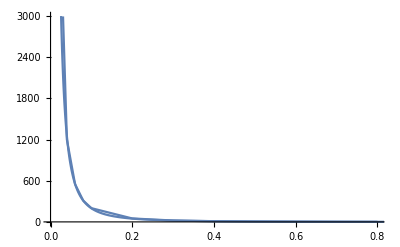

```mathematica
Show[ListLinePlot[{{0.01,20000}, {0.02,5000}, {0.04, 1200}, {0.06, 550}, {0.08, 310}, {0.1, 200}, {0.2, 50}, {0.3, 20}, {0.4, 10}, {0.5, 6}, {0.6, 4}, {0.7, 2}, {0.8, 1}}], Plot[2/m^2-2, {m, 0, 1}, PlotRange->{{0, 1},{0, 3000}}]]
```

```mathematica
Solve[xi==(1-cos)/(1-cos+alpha^2 cos),cos]//FullSimplify
```

{{cos→(1-xi)/(1+(-1+alpha^2) xi)}}

```mathematica
xi=(1-cos)/(1-cos+alpha^2 cos)
```

(1-cos)/(1-cos+alpha^2 cos)

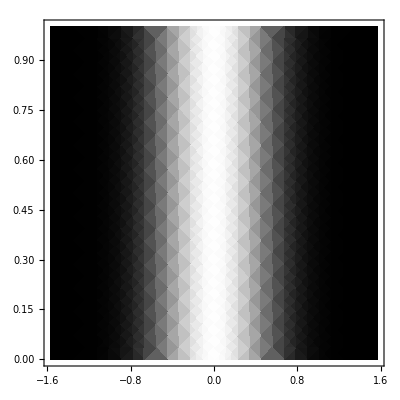

General::munfl: Exp[-7.94358×10^7] is too small to represent as a normalized machine number; precision may be lost.

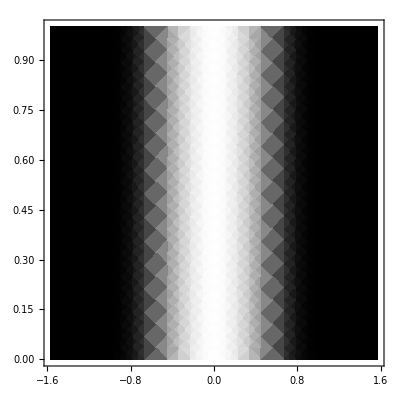

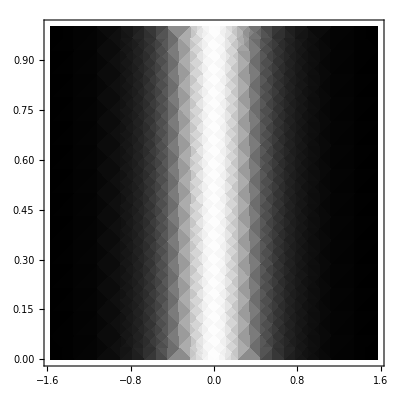

```mathematica
ColorFunc[ z_ ] :=RGBColor[z,z,z];
With[{alpha=0.5},DensityPlot[blinn[theta, 2/alpha^2-2], {theta, -π/2, π/2}, {y, 0, 1},PlotRange->Full,ColorFunction->ColorFunc]]
With[{alpha=0.5},DensityPlot[beckmann[theta,alpha], {theta, -π/2, π/2}, {y, 0, 1},PlotRange->Full,ColorFunction->ColorFunc]]
With[{alpha=0.5},DensityPlot[ggx[theta,alpha], {theta, -π/2, π/2}, {y, 0, 1},PlotRange->Full,ColorFunction->ColorFunc]]
```

```mathematica
FresnelDielectric[etat_]:=(
etai=1;
points={};
For[thetai=0, thetai<=Pi/2, thetai+=Pi/200, 
costhetai=Cos[thetai];
sinthetai=Sqrt[1-costhetai^2];
sinthetat=etai/etat*sinthetai;
costhetat=Sqrt[1-sinthetat^2];
rparl=(etat*costhetai-etai*costhetat)/(etat*costhetai+etai*costhetat);
rperp=(etai*costhetai-etat*costhetat)/(etai*costhetai+etat*costhetat);

AppendTo[points,{thetai, (rparl^2+rperp^2)/2}];
];
points
)

FresnelConductor[etat_, k_]:=(
etai=1;
eta=etat/etai;
etak=k/etai;
points={};
For[thetai=0, thetai<=Pi/2, thetai+=Pi/200, 
costhetai=Cos[thetai];
costhetai2=costhetai^2;
sinthetai2=1-costhetai2;
eta2=eta^2;
etak2=etak^2;
t0=eta2-etak2-sinthetai2;
a2plusb2=Sqrt[t0*t0+4*eta2*etak2];
t1=a2plusb2+costhetai2;
a=Sqrt[0.5*(a2plusb2+t0)];
t2=2*costhetai*a;
rs=(t1-t2)/(t1+t2);
t3=costhetai2*a2plusb2+sinthetai2*sinthetai2;
t4=t2*sinthetai2;
rp=rs*(t3-t4)/(t3+t4);
AppendTo[points, {thetai, 0.5*(rp+rs)}]
];
points

)
```

```mathematica
ListLinePlot[{FresnelDielectric[1.5],FresnelDielectric[2.418],FresnelConductor[0.277, 2.92], FresnelConductor[0.051, 3.9], FresnelConductor[2.93, 3]}, PlotRange->{0,  1.2},Ticks->{Range[0,Pi/2,Pi/8],Automatic},BaseStyle->{FontFamily->"Cambria", FontSize->14, FontSlant->Italic}, AxesStyle->Arrowheads[{0, 0.03}], AxesOrigin->{0, 0},AxesLabel->{"θ_i","F_r(θ_i)"}, PlotStyle->Black, PlotLabels->
{Callout["Стекло",{Scaled[0.15],Above}],
Callout["Алмаз",{Scaled[0.3],Above}],
Callout["Золото",{Scaled[0.5],Above}], 
Callout["Серебро",{Scaled[0.7],Above}],
Callout["Железо",{Scaled[0.4],Above}]}]
```

-Graphics-

0.890914

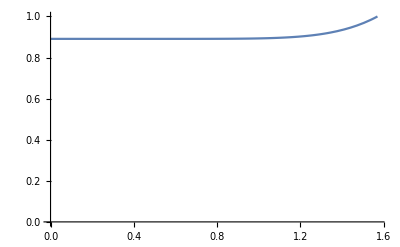

```mathematica
fr0[etat_, k_]:=((etat-1)^2+k^2)/((etat+1)^2+k^2);
f0=fr0[0.277, 2.92]
Plot[f0+(1-f0)*(1-Cos[thetai])^5, {thetai, 0, Pi/2}, PlotRange->{0, 1}]
```

0.172111

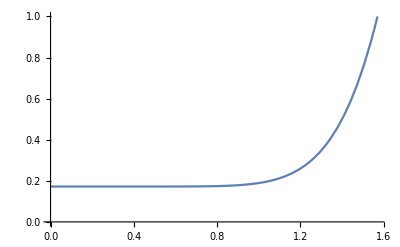

```mathematica
fr0[etat_]:=(etat-1)^2/(etat+1)^2;
f0=fr0[2.418]
Plot[f0+(1-f0)*(1-Cos[thetai])^5, {thetai, 0, Pi/2}, PlotRange->{0, 1}]
```

```mathematica
FullSimplify[(etat-1)^2/(etat+1)^2]
```

(-1+etat)^2/(1+etat)^2

```mathematica
Integrate[(alpha^2 Cos[theta]*Sin[theta])/(π ((alpha^2-1) Cos[theta]^2+1)^2),{theta, 0, theta1}]
```

$Aborted

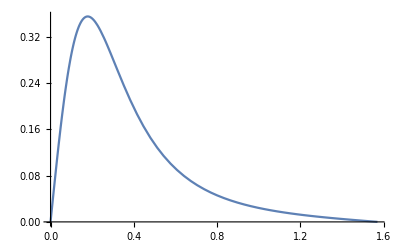

```mathematica
alpha = 0.3;
Plot[(alpha^2*Cos[theta]*Sin[theta])/(π ((alpha^2-1) Cos[theta]^2+1)^2), {theta, 0, Pi/2}]
```